```mathematica
f[x_]:=3.5+√(3.5^2+18x)
```

```mathematica
g[x_]:=(0.001204f[x]^2+0.002408f[x]+18x)^2-4(0.002408f[x]^3+0.043345x*f[x])
```

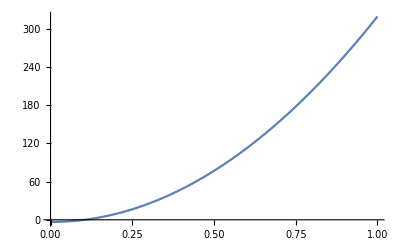

```mathematica
Plot[g[x],{x,0,1}]
```

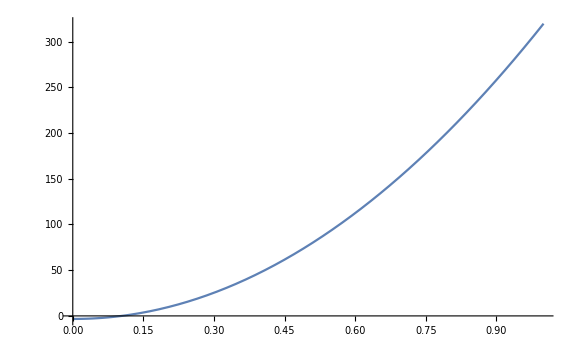

```mathematica
Show[%55,ImageSize->Large]
```

```mathematica
g[x]
```

(18 x+0.002408 (3.5+√(12.25+18 x))+0.001204 (3.5+√(12.25+18 x))^2)^2-4 (0.043345 x (3.5+√(12.25+18 x))+0.002408 (3.5+√(12.25+18 x))^3)

```mathematica
Solve[(18 x+0.002408 (3.5+√(12.25+18 x))+0.001204 (3.5+√(12.25+18 x))^2)^2-4 (0.043345 x (3.5+√(12.25+18 x))+0.002408 (3.5+√(12.25+18 x))^3)==0,x]
```

{{x→-0.0974779},{x→0.103995}}